```mathematica
(*反時計まわりが正か負か，人によってことなる．
反時計回りが正のことが多いようなので，ここでもそのように決める*)
```

### 回転行列

```mathematica
Clear["Global`*"];
Import[FileNameJoin[{NotebookDirectory[],"LibQuaternionRotation.m"}]]
```

```mathematica
(*磁場センサーのキャリブレーション*)
(*InitM= {InitMx,InitMy,InitMz}*)
{bx,by,bz}={1.22,1.32,0.62}
{Mx0,My0,Mz0}={-11.54,-12.3,-8.2}
{Mx1,My1,Mz1}={-11.8,-12.6,-4.1}
{Mx2,My2,Mz2}={-14.6,-8.1,-4.8}

InitM={Mx0,My0,Mz0}; {InitMx,InitMy,InitMz}

InvRs0=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},0/180*Pi]]
InvRs1=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},120/180*Pi]]
InvRs2=Inverse@Rs[AxisAngleToQuaternion[{1,1,1},240/180*Pi]]

Mb[{Mx_,My_,Mz_}]:={
{Mx-bx,My-by,Mz-bz,0,0,0,0,0,0},
{0,0,0,Mx-bx,My-by,Mz-bz,0,0,0},
{0,0,0,0,0,0,Mx-bx,My-by,Mz-bz}}

MatrxMb=Join[
Mb[{Mx0,My0,Mz0}],
Mb[{Mx1,My1,Mz1}],
Mb[{Mx2,My2,Mz2}]]

RsInitM=Join[
Dot[InvRs0,InitM],
Dot[InvRs1,InitM],
Dot[InvRs2,InitM]]

FullSimplify@Dot[Inverse[MatrxMb],RsInitM]
```

{1.22,1.32,0.62}

{-11.54,-12.3,-8.2}

{-11.8,-12.6,-4.1}

{-14.6,-8.1,-4.8}

{InitMx,InitMy,InitMz}

{{1,0,0},{0,1,0},{0,0,1}}

{{0,1,0},{0,0,1},{1,0,0}}

{{0,0,1},{1,0,0},{0,1,0}}

{{-12.76,-13.62,-8.82,0,0,0,0,0,0},{0,0,0,-12.76,-13.62,-8.82,0,0,0},{0,0,0,0,0,0,-12.76,-13.62,-8.82},{-13.02,-13.92,-4.72,0,0,0,0,0,0},{0,0,0,-13.02,-13.92,-4.72,0,0,0},{0,0,0,0,0,0,-13.02,-13.92,-4.72},{-15.82,-9.42,-5.42,0,0,0,0,0,0},{0,0,0,-15.82,-9.42,-5.42,0,0,0},{0,0,0,0,0,0,-15.82,-9.42,-5.42}}

{-11.54,-12.3,-8.2,-12.3,-8.2,-11.54,-8.2,-11.54,-12.3}

{0.0197872,0.905085,-0.117885,0.532323,-0.253073,1.01524,0.875692,0.260873,-0.740014}

### 姿勢の計算の関数

```mathematica
(*満たすべき方程式*)
Q=Table[q[i],{i,0,3,1}];
{v0[0],v0[1],v0[2],v0[3],v0[4],v0[5]}={gx0,gy0,gz0,mx0,my0,mz0};(*物体の加速度を無視し，重力加速度だけがかかっている．実際は{gx0,gy0,gz0}に物体の加速度がかかっている*)
{u[0],u[1],u[2],u[3],u[4],u[5]}={Ax,Ay,Az,Mx,My,Mz};(*sensor value*)

Print["RR(q)=RR({a,b,c,d})=",RR[{a,b,c,d}]//MatrixForm]
(*関数*)

originalEq[{a_,b_,c_,d_}]=Module[{},
Table[(u[i]-Sum[RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}]
];

rep={a^2->a2,b^2->b2,d^2->d2,c^2->c2,
a^3->a3,b^3->b3,d^3->d3,c^3->c2,
(a2 + b2 + c2 + d2)->a2b2c2d2,
u0^2->u02,u1^2->u12,u2^2->u22,u3^2->u32,u4^2->u42,u5^2->u52,gx0^2+gy0^2+gz0^2+mx0^2+my0^2+mz0^2->normGM2,Power->pow};

CForm[FullSimplify[originalEq[{a,b,c,d}]]]/.rep/.rep/.Power->pow


f[{a_,b_,c_,d_}]=Sum[(u[i]-Sum[
RR[{a,b,c,d}][[i+1]][[j+1]]*v0[j],{j,0,5,1}])^2,{i,0,5,1}]/4(*+(1-Sqrt[a^2+b^2+c^2+d^2])*);
(*最小にする関数の微分*)
F[{a_,b_,c_,d_}]=Simplify@{
D[f[{A,b,c,d}],A]/.{A->a},
D[f[{a,B,c,d}],B]/.{B->b},
D[f[{a,b,C,d}],C]/.{C->c},
D[f[{a,b,c,dd}],dd]/.{dd->d}
};
(*最小にする関数の微分の微分*)
DF[{a_,b_,c_,d_}]=Simplify[{
D[F[{A,b,c,d}],A]/.{A->a},
D[F[{a,B,c,d}],B]/.{B->b},
D[F[{a,b,C,d}],C]/.{C->c},
D[F[{a,b,c,dd}],dd]/.{dd->d}}];

Fmod[{a_,b_,c_,d_},A_,M_]:=F[{a,b,c,d}]/.{Ax->A[[1]],Ay->A[[2]],Az->A[[3]],Mx->M[[1]],My->M[[2]],Mz->M[[3]]}
DFmod[{a_,b_,c_,d_},A_,M_]:=DF[{a,b,c,d}]/.{Ax->A[[1]],Ay->A[[2]],Az->A[[3]],Mx->M[[1]],My->M[[2]],Mz->M[[3]]}
```

RR(q)=RR({a,b,c,d})=(a^2+b^2-c^2-d^2 | 2 b c+2 a d | -2 a c+2 b d | 0 | 0 | 0
2 b c-2 a d | a^2-b^2+c^2-d^2 | 2 a b+2 c d | 0 | 0 | 0
2 a c+2 b d | -2 a b+2 c d | a^2-b^2-c^2+d^2 | 0 | 0 | 0
0 | 0 | 0 | a^2+b^2-c^2-d^2 | 2 b c+2 a d | -2 a c+2 b d
0 | 0 | 0 | 2 b c-2 a d | a^2-b^2+c^2-d^2 | 2 a b+2 c d
0 | 0 | 0 | 2 a c+2 b d | -2 a b+2 c d | a^2-b^2-c^2+d^2)

List(pow(Ax - a2*gx0 - b2*gx0 + (c2 + d2)*gx0 + a*(-2*d*gy0 + 2*c*gz0) - 2*b*(c*gy0 + d*gz0),2),
   pow(Ay + 2*a*d*gx0 - a2*gy0 + b2*gy0 - c2*gy0 + d2*gy0 - 2*c*d*gz0 - 2*b*(c*gx0 + a*gz0),2),
   pow(Az - 2*(a*c*gx0 + b*d*gx0 - a*b*gy0 + c*d*gy0) + (-a2 + b2 + c2 - d2)*gz0,2),
   pow(Mx - a2*mx0 - b2*mx0 + (c2 + d2)*mx0 + a*(-2*d*my0 + 2*c*mz0) - 2*b*(c*my0 + d*mz0),2),
   pow(2*a*d*mx0 + My - a2*my0 + b2*my0 - c2*my0 + d2*my0 - 2*c*d*mz0 - 2*b*(c*mx0 + a*mz0),2),
   pow(-2*(a*c*mx0 + b*d*mx0 - a*b*my0 + c*d*my0) + Mz + (-a2 + b2 + c2 - d2)*mz0,2))

```mathematica
yaw[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*d+b*c)/(1-2*(c*c+d*d))]
roll[{a_,b_,c_,d_}]:=N@ArcTan[2*(a*b+c*d)/(1-2*(b*b+c*c))]
pitch[{a_,b_,c_,d_}]:=N@ArcSin[2*(a*c-b*d)]
```

### チェック

```mathematica
(*Clear[a,b,c,d]
Print["空間を回転させる回転行列"]
Print[CForm[Rs[{a,b,c,d}]/.rep]]
Print["空間を固定しベクトルを回転させる回転行列"]
Print[CForm[Transpose[Rs[{a,b,c,d}]/.rep]]]
N@R[Normalize@{4,1,2,3}]*)
```

### 姿勢の計算

```mathematica
(*.08加速度をいっぺんに計算する*)
```

```mathematica
(*データの読み込み*)
```

```mathematica
(*imported =Import[FileNameJoin["/Users/tomoaki/Dropbox/markdown/python_shared/example_AHRS/dataAHRS.json"]];*)
imported =Import[FileNameJoin[{NotebookDirectory[],"dataAHRS.json"}]];
Column@imported[[1]](*例*)
rowGyros=ParallelTable[("mag"/.#5)&@@imported[[i]],{i,1,Length[imported]}];
```

period→0.001
gyro→{-0.0381679,-0.114504,-0.0305344}
accel→{0.0327148,-0.0424805,-1.00903}
dt→0.014457
mag→{0.37384,2.07855,2.258}
time_ns→4094123268000

```mathematica
{minmaxX,minmaxY,minmaxZ}=CoordinateBounds[rowGyros];
magCenterX=Mean[minmaxX]
magCenterY=Mean[minmaxY]
magCenterZ=Mean[minmaxZ]
magCenterXYZ={magCenterX,magCenterY,magCenterZ};

(*初期姿勢の静止姿勢で観測される重力加速度と磁場を設定．これはfusionの初期に一つ決める値で，DFやFに組み込まれる*)
magBias={-2.044069644509259,3.296398226566499,2.029526850118487}-magCenterXYZ;gyroBias={-0.454917765991497,-0.12121859207787493,-0.09516749018618002};
accelBias={0.014670909915040676,0.11165143283325697,-1.0097354621661374};
(****************************************************)
(*θ=-54/180*Pi;
{gx0,gy0,gz0}={0,0,-1};(*g0*)
{mx0,my0,mz0}={Cos[θ],0,Sin[θ]};(*m0*)
*)

{gx0,gy0,gz0}=accelBias;(*g0*)
{mx0,my0,mz0}=magBias;(*m0*)
(****************************************************)
{a,b,c,d}={RandomReal[],RandomReal[],RandomReal[],RandomReal[]};
getQuaternion[A0_,M0_,Q_]:=Module[{data,abcd,dq,DQ,Ax,Ay,Az,Mx,My,Mz,a,b,c,d,M,A},
M=Normalize@M0;
A=Normalize@A0;
{a,b,c,d}=Normalize@Q;
dq={1,0,0,0};
Do[
dq=(Dot[Inverse[DFmod[{a,b,c,d},A,M]],Fmod[{a,b,c,d},A,M]]);
{a,b,c,d}-=dq;
{a,b,c,d}=Normalize[{a,b,c,d}];
If[Abs[dq]<10^-7,Break;];
,{i,0,15,1}];
Return[{a,b,c,d}];
]
```

-1.48041

1.71967

4.04495

### シミュレーション

```mathematica
P={};
W={};
A={};
Abody={};
AbodyAccum={};
AbodyByApproxQ={};
AbodyByCombinedQ={};
AXRawer=AYRawer=AZRawer={};
AXRaw=AYRaw=AZRaw={};

dT={};
T={};
M=MX=MY=MZ={};
W=WX=WY=WZ={};
Q={};
q={RandomReal[],RandomReal[],RandomReal[],RandomReal[]};
starttime=("time_ns"/.#6)*10^-9&@@imported[[1]]

w=a=aRawer={0,0,0};
t=0;
abody=abodyAccum=abodyByApproxQ=abodyByCombinedQ={0,0,0};
m={0,0,0};
α=1.;
αraw=1.;
β=1.;
γ=1.;
(*シミュレーション*)
Do[
data=imported[[i]];
{p,dt,rowgyro,rowaccel,rowmag,timens}={"period","dt","gyro","accel","mag","time_ns"}/.data;
lastw=w;
w=γ*(rowgyro-gyroBias)+(1-γ)*w;
a=α*(rowaccel)+(1-α)*a;
aRawer=αraw*(rowaccel)+(1-αraw)*aRawer;
m=β*(rowmag-magCenterXYZ)+(1-β)*m;
remotedt=timens*10^-9-starttime-t;
t=timens*10^-9-starttime;

(*Print[p,w,a,dt,m,t,remotedt,dQdt[q,w]];*)
approxq=Normalize[(q+remotedt*dQdt[q,w])];

q=Normalize[Quiet@getQuaternion[a,m,q]];

abody=(aRawer-Dot[Rs[q],{0,0,-1}]);

abodyAccum=0.8*abodyAccum+0.2*abody;

abodyByApproxQ=(aRawer-Dot[Rs[approxq],{0,0,-1}]);

c=0.5;
CombinedQ=Normalize[((1-c)*approxq+c*q)];
abodyByCombinedQ=(aRawer-Dot[Rs[CombinedQ],{0,0,-1}]);

(*q=CombinedQ;*)

AppendTo[P,p];
AppendTo[W,w];
AppendTo[A,a];
AppendTo[Abody,abody];
AppendTo[AbodyAccum,abodyAccum];
AppendTo[AbodyByApproxQ,abodyByApproxQ];
AppendTo[AbodyByCombinedQ,abodyByCombinedQ];
AppendTo[AXRawer,aRawer[[1]]];
AppendTo[AYRawer,aRawer[[2]]];
AppendTo[AZRawer,aRawer[[3]]];
AppendTo[AXRaw,rowaccel[[1]]];
AppendTo[AYRaw,rowaccel[[2]]];
AppendTo[AZRaw,rowaccel[[3]]];
AppendTo[M,m];
AppendTo[MX,m[[1]]];
AppendTo[MY,m[[2]]];
AppendTo[MZ,m[[3]]];
AppendTo[WX,w[[1]]];
AppendTo[WY,w[[2]]];
AppendTo[WZ,w[[3]]];
AppendTo[T,t];
AppendTo[Q,q];
,{i,1,Length[imported]}]
```

1023530817/250000

```mathematica
intpX=Interpolation[Table[{T[[i]],A[[i]][[1]]},{i,1,Length[Q]}],InterpolationOrder->1];
intpY=Interpolation[Table[{T[[i]],A[[i]][[2]]},{i,1,Length[Q]}],InterpolationOrder->1];
intpZ=Interpolation[Table[{T[[i]],A[[i]][[3]]},{i,1,Length[Q]}],InterpolationOrder->1];
```

```mathematica
LowPassFilter[data_,w_]:=Module[{intp,DATA,n,st,et,sr,wn,DATALPF},
n=Length[data];
st=data[[1]][[1]];
et=data[[Length[data]]][[1]];
sr=N@(et-st)/(n-1)(*sec/num*);
w(*1/sec*);
wn=sr/w(*sec/num/sec=1/num*);
Print["st=",st,",et=",N@et,", sample rate=",sr,", wn=",wn];
intp=Interpolation[Table[{data[[i]][[1]],data[[i]][[2]]},{i,1,Length[data]}],InterpolationOrder->1];
DATA=Table[{t,intp[t]},{t,Subdivide[st,et,n-1]}];
DATALPF=LowpassFilter[Transpose[DATA][[2]],wn,SampleRate->1];
Return[Table[{DATA[[i]][[1]],DATALPF[[i]]},{i,1,Length[DATALPF]}]];
];

LowPassFilterNDim[data_,w_]:=Module[{intp,DATA,n,st,et,sr,wn,DATALPF,l,dataT,v,vT,T,res,resT},
l=Length[data[[1]][[2]]];
v=Table[data[[i]][[2]],{i,1,Length[data],1}];
T=Table[data[[i]][[1]],{i,1,Length[data],1}];
vT=Transpose[v];
res=Table[LowPassFilter[Table[{T[[t]],vT[[i]][[t]]},{t,1,Length[data],1}],w],{i,1,l,1}];
resT=Transpose[res];
Return@Table[{resT[[t]][[1]][[1]],Table[resT[[t]][[i]][[2]],{i,1,l,1}]},{t,1,Length[resT],1}];
(*Return[res];*)
(*Return[Table[res[[1]][[t]],Table[res[[k]][[t]],{k,1,l,1}],{t,1,Length[res[[1]]],1}]];*)
];
```

```mathematica
(*T=10;
data=Table[{t,Cos[(2π/T*t)*(2π/T*t)]+RandomReal[]},{t,0,2*T,.01}];
ListPlot[data,PlotRange->All]
dataLPF=LowPassFilter[data,2π/T/5];
ListPlot[{data,dataLPF},PlotRange->All]

Periodogram[{Transpose[data][[2]],Transpose[dataLPF][[2]]}]*)
```

```mathematica
ListPointPlot3D[Table[{T[[i]],M[[i]]},{i,1,Length[T]}],BoxRatios->{1, 1, 1},PlotLabel->"磁気データ"]
ListPointPlot3D[Table[{T[[i]],A[[i]]},{i,1,Length[T]}],BoxRatios->{1, 1, 1},PlotLabel->"加速度データ"]
```

-Graphics3D-

-Graphics3D-

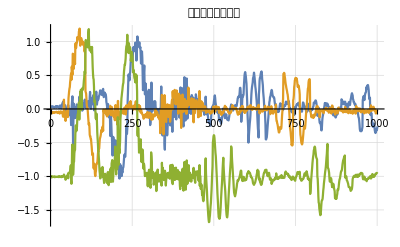

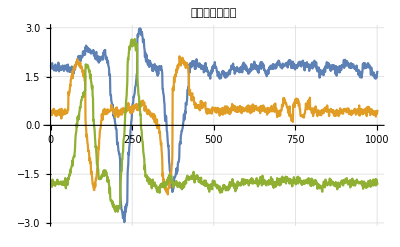

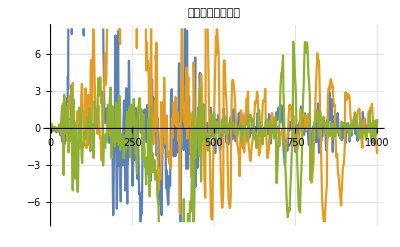

```mathematica
ListPlot[{AXRaw,AYRaw,AZRaw},Joined->True,PlotLabel->"加速度成分データ",PlotRange->Automatic,GridLines->Automatic]
ListPlot[{MX,MY,MZ},Joined->True,PlotLabel->"磁場成分データ",PlotRange->Automatic,GridLines->Automatic]
ListPlot[{WX,WY,WZ},Joined->True,PlotLabel->"角速度成分データ",PlotRange->Automatic,GridLines->Automatic]

accelXYZ=Transpose@{AXRaw,AYRaw,AZRaw};

accelX=Table[{T[[i]],accelXYZ[[i]][[1]]},{i,1,Length[accelXYZ]}];
accelY=Table[{T[[i]],accelXYZ[[i]][[2]]},{i,1,Length[accelXYZ]}];
accelZ=Table[{T[[i]],accelXYZ[[i]][[3]]},{i,1,Length[accelXYZ]}];

magXYZ=M;
magX=Table[{T[[i]],magXYZ[[i]][[1]]},{i,1,Length[magXYZ]}];
magY=Table[{T[[i]],magXYZ[[i]][[2]]},{i,1,Length[magXYZ]}];
magZ=Table[{T[[i]],magXYZ[[i]][[3]]},{i,1,Length[magXYZ]}];

gyroXYZ=W;
gyroX=Table[{T[[i]],gyroXYZ[[i]][[1]]},{i,1,Length[gyroXYZ]}];
gyroY=Table[{T[[i]],gyroXYZ[[i]][[2]]},{i,1,Length[gyroXYZ]}];
gyroZ=Table[{T[[i]],gyroXYZ[[i]][[3]]},{i,1,Length[gyroXYZ]}];
```

st=0,et=19.8091, sample rate=0.0198091, wn=0.198091

st=0,et=19.8091, sample rate=0.0198091, wn=0.198091

st=0,et=19.8091, sample rate=0.0198091, wn=0.198091

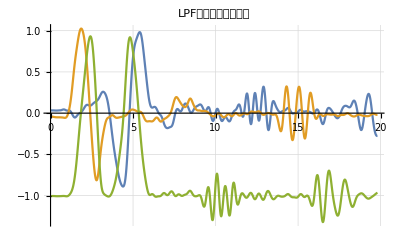

st=0,et=19.8091, sample rate=0.0198091, wn=0.396181

st=0,et=19.8091, sample rate=0.0198091, wn=0.396181

st=0,et=19.8091, sample rate=0.0198091, wn=0.396181

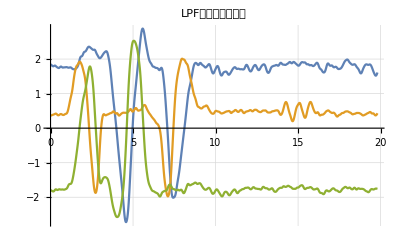

st=0,et=19.8091, sample rate=0.0198091, wn=0.396181

st=0,et=19.8091, sample rate=0.0198091, wn=0.396181

st=0,et=19.8091, sample rate=0.0198091, wn=0.396181

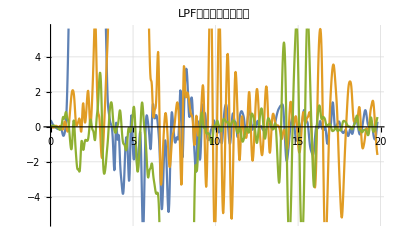

st=0,et=19.8091, sample rate=0.0198091, wn=19.8091

st=0,et=19.8091, sample rate=0.0198091, wn=0.198091

st=0,et=19.8091, sample rate=0.0198091, wn=0.198091

st=0,et=19.8091, sample rate=0.0198091, wn=0.198091

st=0,et=19.8091, sample rate=0.0198091, wn=0.396181

st=0,et=19.8091, sample rate=0.0198091, wn=0.396181

st=0,et=19.8091, sample rate=0.0198091, wn=0.396181

```mathematica
(*カットオフ周波数を設定*)
cutoffAccel=0.1;
cutoffMag=0.05;
cutoffGyro=0.05;

ListPlot[{
LowPassFilter[accelX,cutoffAccel],
LowPassFilter[accelY,cutoffAccel],
LowPassFilter[accelZ,cutoffAccel]},Joined->True,PlotLabel->"LPF加速度成分データ",PlotRange->Automatic,GridLines->Automatic]

ListPlot[{
LowPassFilter[magX,cutoffMag],
LowPassFilter[magY,cutoffMag],
LowPassFilter[magZ,cutoffMag]},Joined->True,PlotLabel->"LPF磁場成分データ",PlotRange->Automatic,GridLines->Automatic]

ListPlot[{
LowPassFilter[gyroX,cutoffGyro],
LowPassFilter[gyroY,cutoffGyro],
LowPassFilter[gyroZ,cutoffGyro]},Joined->True,PlotLabel->"LPF角速度成分データ",PlotRange->Automatic,GridLines->Automatic]


(*TaccelXLPF=LowPassFilter[accelX,0.001];*)
TimeForLPF=Transpose[LowPassFilter[accelX,0.001]][[1]];
accelXYZLPF=Transpose@{
Transpose[LowPassFilter[accelX,cutoffAccel]][[2]],
Transpose[LowPassFilter[accelY,cutoffAccel]][[2]],
Transpose[LowPassFilter[accelZ,cutoffAccel]][[2]]
};
magXYZLPF=Transpose@{
Transpose[LowPassFilter[magX,cutoffMag]][[2]],
Transpose[LowPassFilter[magY,cutoffMag]][[2]],
Transpose[LowPassFilter[magZ,cutoffMag]][[2]]
};
```

```mathematica
intpAX=Interpolation[LowPassFilter[Table[{T[[i]],A[[i]][[1]]},{i,1,Length[A]}],0.05],InterpolationOrder->1];
intpAY=Interpolation[LowPassFilter[Table[{T[[i]],A[[i]][[2]]},{i,1,Length[A]}],0.05],InterpolationOrder->1];
intpAZ=Interpolation[LowPassFilter[Table[{T[[i]],A[[i]][[3]]},{i,1,Length[A]}],0.05],InterpolationOrder->1];
```

st=0,et=19.8091, sample rate=0.0198091, wn=0.396181

st=0,et=19.8091, sample rate=0.0198091, wn=0.396181

st=0,et=19.8091, sample rate=0.0198091, wn=0.396181

```mathematica
ExtractTV[data_,i_]:=Module[{},Return[Table[{data[[j]][[1]],data[[j]][[2]][[i]]},{j,1,Length[data],1}]];]
```

#### 標準的な方法でqを計算

```mathematica
Quaternions=QuaternionsT={};
t=dt=0;
(*標準的な方法でqを計算*)
Do[
If[i>1,dt=TimeForLPF[[i]]-TimeForLPF[[i-1]]];
approxq=Normalize[(q+dt*dQdt[q,w])];
q=Normalize[Quiet@getQuaternion[accelXYZLPF[[i]],magXYZLPF[[i]],approxq]];
(*q=Normalize[10q+approxq];*)
t=TimeForLPF[[i]];
AppendTo[Quaternions,q];
AppendTo[QuaternionsT,{t,q}];
,{i,1,Length[accelXYZLPF]}]
```

#### クォータニオンをLPF

```mathematica
(*クォータニオンをLPF*)
cutoffQ=0.1;
QuaternionsTLPF=LowPassFilterNDim[QuaternionsT,cutoffQ];
```

st=0,et=19.8091, sample rate=0.0198091, wn=0.198091

st=0,et=19.8091, sample rate=0.0198091, wn=0.198091

st=0,et=19.8091, sample rate=0.0198091, wn=0.198091

«1 more identical outputs»

#### LPFしたqを使って物体の加速度を計算

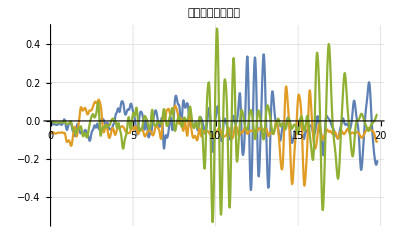

-Graphics-

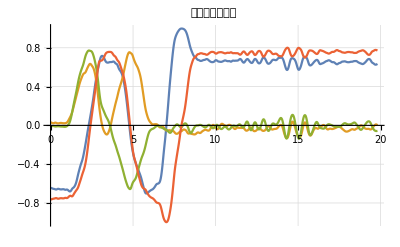

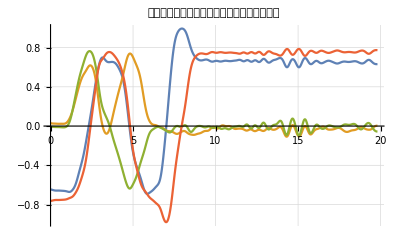

```mathematica
q=approxq={0,0,0,0};
abody={0,0,0};
AssumedAbodyX=AssumedAbodyY=AssumedAbodyZ=AssumedAbody={};
AssumedAbodyXT=AssumedAbodyYT=AssumedAbodyZT={};
Abody=AbodyXT=AbodyYT=AbodyZT={};
Do[
If[i>2,
dt=QuaternionsTLPF[[i]][[1]]-QuaternionsTLPF[[i-1]][[1]];
w=(magXYZLPF[[i]]+magXYZLPF[[i-2]])/2;
approxq=Normalize[(q+dt*dQdt[q,w])];
];
q=Normalize[approxq/10+QuaternionsTLPF[[i]][[2]]];
t=QuaternionsTLPF[[i]][[1]];

abody=({intpAX[t],intpAY[t],intpAZ[t]}-Dot[Rs[q],{0,0,-1}]);
assumedabody=({intpAX[t],intpAY[t],intpAZ[t]}-Dot[Rs[q],{0,0,-1}]);

AppendTo[Abody,abody];
AppendTo[AssumedAbodyX,assumedabody[[1]]];
AppendTo[AssumedAbodyY,assumedabody[[2]]];
AppendTo[AssumedAbodyZ,assumedabody[[3]]];
AppendTo[AssumedAbodyXT,{t,assumedabody[[1]]}];
AppendTo[AssumedAbodyYT,{t,assumedabody[[2]]}];
AppendTo[AssumedAbodyZT,{t,assumedabody[[3]]}];
AppendTo[AbodyXT,{t,abody[[1]]}];
AppendTo[AbodyYT,{t,abody[[2]]}];
AppendTo[AbodyZT,{t,abody[[3]]}];
,{i,1,Length[QuaternionsTLPF]}]

ListPlot[{AbodyXT,AbodyYT,AbodyZT},Joined->True,PlotLabel->"物体の加速度成分",PlotRange->{All,All},GridLines->Automatic]
ListPlot[{AssumedAbodyXT,AssumedAbodyYT,AssumedAbodyZT},Joined->True,PlotLabel->"物体の加速度成分",PlotRange->{All,All},GridLines->Automatic]
ListPlot[Table[ExtractTV[QuaternionsT,i],{i,1,4,1}],Joined->True,PlotLabel->"クォータニオン",PlotRange->{All,All},GridLines->Automatic]
ListPlot[Table[ExtractTV[QuaternionsTLPF,i],{i,1,4,1}],Joined->True,PlotLabel->"ローパスフィルターを施したクォータニオン",PlotRange->{All,All},GridLines->Automatic]
```

```mathematica
arrowAxes[arrowLength_]:=Map[{Apply[RGBColor,#],Arrow[Tube[{{0,0,0},#}]]}&,arrowLength IdentityMatrix[3]]

ship=ExampleData[{"Geometry3D","Galleon"},"GraphicsComplex"];
tab=Table[
Module[{t},
t=N@QuaternionsTLPF[[i]][[1]];
Graphics3D[{
GeometricTransformation[ship,Rs[QuaternionsTLPF[[i]][[2]]]],
arrowAxes[40]
},
PlotLabel->Text[Style[StringForm["t=``",N[t,3]],Blue,Italic,24]],
Axes->True,
Boxed->False,
AxesOrigin->{0,0,0},
AxesStyle->Opacity[0],
TicksStyle->Opacity[1],
PlotRange->Table[{-40,40},{j,1,3,1}]]
],{i,1,Length[QuaternionsTLPF],1}];
Manipulate[
tab[[i]]
,{i,1,Length[QuaternionsTLPF],1}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"anim.gif"}],
Table[tab[[i]],{i,1,Length[tab],Round[Length[tab]/10]}],
"DisplayDurations"->0.1,ImageSize->{500,500}]
```

st=0,et=19.8091, sample rate=0.0198091, wn=1.98091

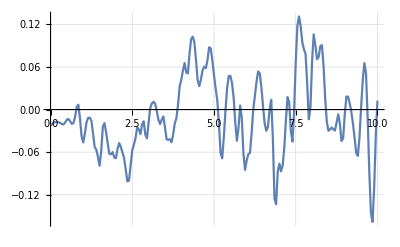

st=0,et=19.8091, sample rate=0.0198091, wn=1.98091

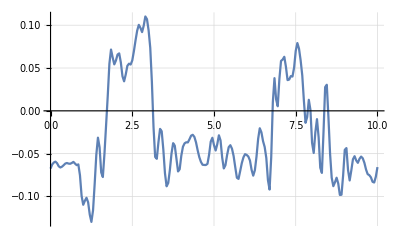

st=0,et=19.8091, sample rate=0.0198091, wn=1.98091

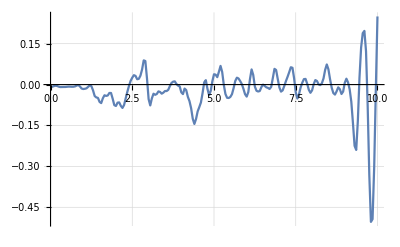

```mathematica
endtime=10;
intpX=Interpolation[LowPassFilter[AbodyXT,0.01],InterpolationOrder->1];
ListPlot[ParallelTable[{x,intpX[x]},{x,0,endtime,.05}],Joined->True,PlotRange->{Automatic,All},GridLines->Automatic]
intpY=Interpolation[LowPassFilter[AbodyYT,0.01],InterpolationOrder->1];
ListPlot[ParallelTable[{x,intpY[x]},{x,0,endtime,.05}],Joined->True,PlotRange->{Automatic,All},GridLines->Automatic]
intpZ=Interpolation[LowPassFilter[AbodyZT,0.01],InterpolationOrder->1];
ListPlot[ParallelTable[{x,intpZ[x]},{x,0,endtime,.05}],Joined->True,PlotRange->{Automatic,All},GridLines->Automatic]
```

-0.0097727

-0.040119

-0.016902

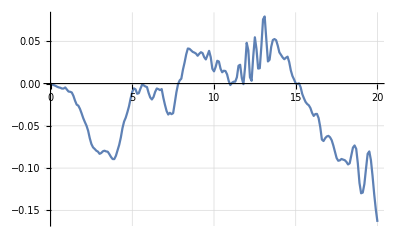

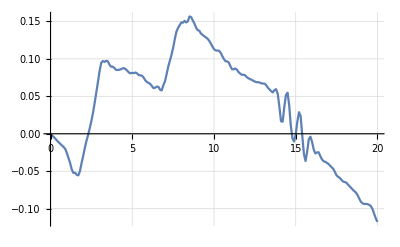

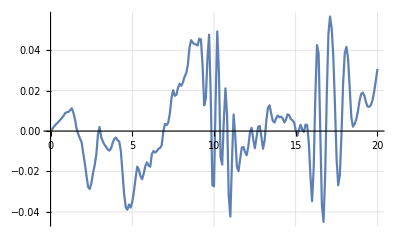

```mathematica
meaX=Mean[Table[intpX[t],{t,0,15,0.01}]]
meaY=Mean[Table[intpY[t],{t,0,15,0.01}]]
meaZ=Mean[Table[intpZ[t],{t,0,15,0.01}]]

ListPlot[ParallelTable[{x,Quiet@NIntegrate[intpX[t]-meaX,{t,0.,x},Method->"TrapezoidalRule"]},{x,0,20,.1}],Joined->True,PlotRange->{Automatic,All},GridLines->Automatic]
ListPlot[ParallelTable[{x,Quiet@NIntegrate[intpY[t]-meaY,{t,0.,x},Method->"TrapezoidalRule"]},{x,0,20,.1}],Joined->True,PlotRange->{Automatic,All},GridLines->Automatic]
ListPlot[ParallelTable[{x,Quiet@NIntegrate[intpZ[t]-meaZ,{t,0.,x},Method->"TrapezoidalRule"]},{x,0,20,.1}],Joined->True,PlotRange->{Automatic,All},GridLines->Automatic]
```

```mathematica
(*ListPlot[ParallelTable[{end,NIntegrate[intpX[x],{x,0,end}]},{end,0,20,.3}],Joined->True]
ListPlot[ParallelTable[{end,NIntegrate[intpY[x],{x,0,end}]},{end,0,20,.3}],Joined->True]
ListPlot[ParallelTable[{end,NIntegrate[intpZ[x],{x,0,end}]},{end,0,20,.3}],Joined->True]*)
```